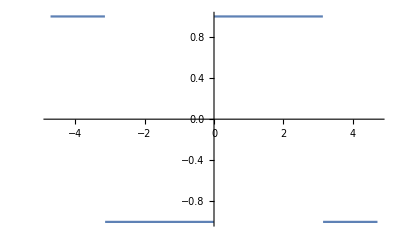

```mathematica
Plot[SquareWave[{-1,1}, x/(2*Pi)], {x, -3*Pi/2, 3*Pi/2}]
```

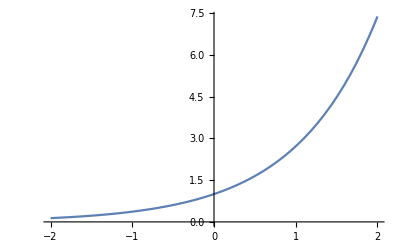

```mathematica
p = Plot[Exp[x],{x, -2,2}]
```

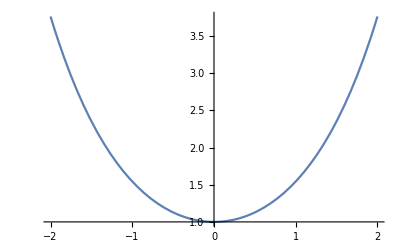

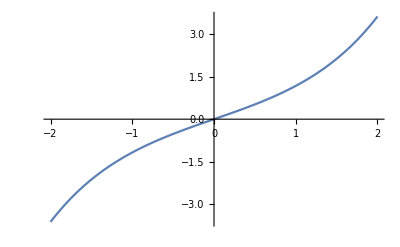

-Graphics-

```mathematica
f[x_]:= Exp[x];
geven[x_] := (f[x] + f[-x])/2;
godd[x_] := (f[x] - f[-x])/2;
Plot[geven[x],{x, -2, 2}]
Plot[godd[x],{x, -2, 2}]
Plot[geven[x] + godd[x],{x, -2, 2}]
```

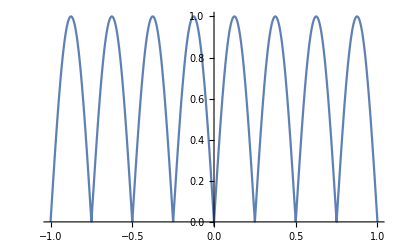

```mathematica
Plot[Abs[Sin[4*Pi*t]], {t,-1,1}]
```

```mathematica
Integrate[Sin[x]^2, x]
```

x/2-1/4 Sin[2 x]

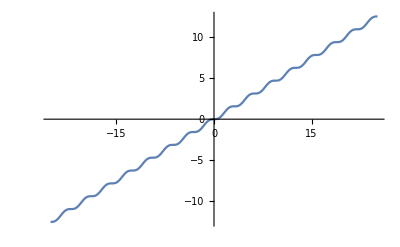

```mathematica
Plot[x/2-1/4 Sin[2 x],{x,-8 π,8 π}]
```

```mathematica
Integrate[Cos[x]^2, x]
```

x/2+1/4 Sin[2 x]

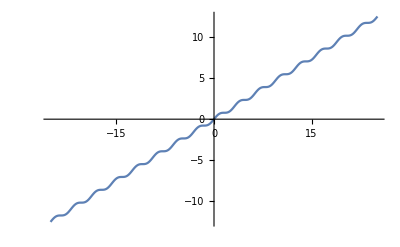

```mathematica
Plot[x/2+1/4 Sin[2 x],{x,-8 π,8 π}]
```

```mathematica
Abs[x]
```

Abs[x]

```mathematica
Integrate[t, t]
```

t^2/2

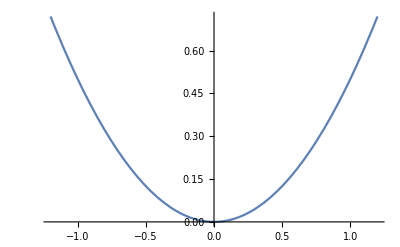

```mathematica
Plot[t^2/2,{t,-1.2,1.2}]
```

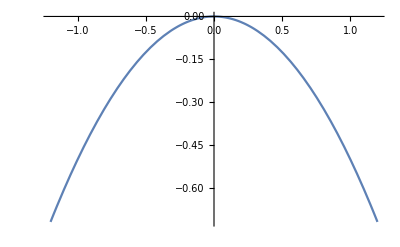

```mathematica
Plot[-t^2/2,{t,-1.2,1.2}]
```

```mathematica
Integrate[1,x]
```

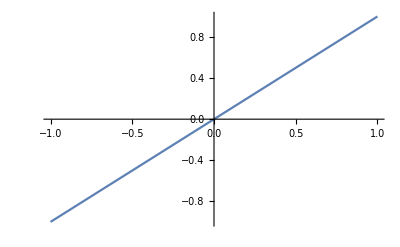

```mathematica
Plot[x, {x, -1, 1}]
```

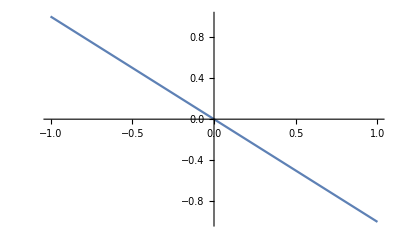

```mathematica
Plot[-x,{x,-1,1}]
```

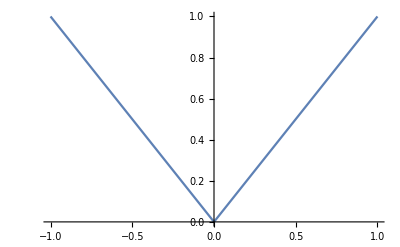

```mathematica
Plot[Abs[t], {t,-1,1}]
```

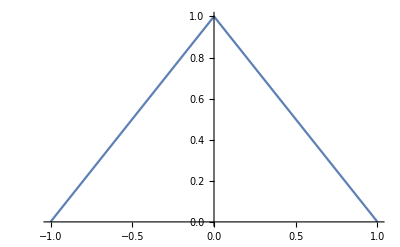

```mathematica
Plot[Abs[Abs[t]-1],{t,-1,1}]
```

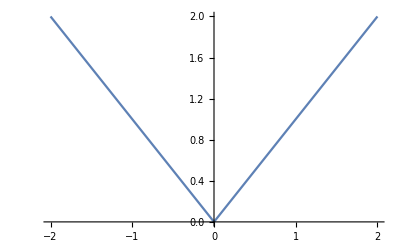

```mathematica
Plot[{Abs[x],-1<x<1},{x,-2,2}]
```

```mathematica
tt[t_] := Abs[t];
hh[t_] := tt[Abs[t]-1];
Plot[hh[t], {t,-1,1}]
```

-Graphics-

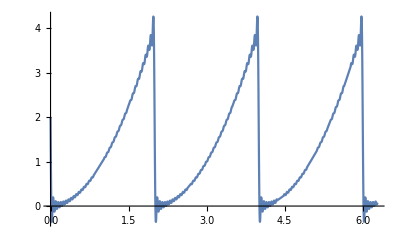

```mathematica
Plot[4/3+Sum[4/Pi^2*Cos[n*Pi*t]/n^2,{n,1, 40}]-Sum[4/Pi*Sin[n*Pi*t]/n,{n,1,40}], {t, 0,2*Pi}]
```

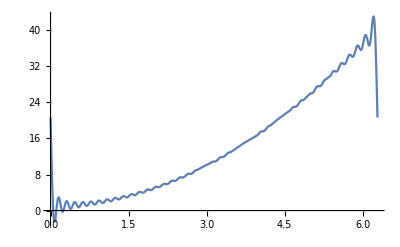

```mathematica
Plot[1+Pi^2*(4/3+Sum[4/Pi^2*Cos[n*t]/n^2,{n,1, 40}]-Sum[4/Pi*Sin[n*t]/n,{n,1,40}]), {t, 0,2*Pi}]
```